```mathematica
Clear["Global`*"]
```

## Distribution of X(t+1) given {X_i(t)}

```mathematica
h[z] = ((1+fN)^n Con^n z^n)/(k^n + (1+fN)^n Con^n z^n);
e1=Integrate[ h[z] /. {n-> 2}, {z,0,1}, Assumptions->{fN ∈ Reals, k∈ Reals,Con∈ Reals,fN>0, k>0, Con>1}]
```

1-(k ArcTan[(Con+Con fN)/k])/(Con+Con fN)

```mathematica
e2=Integrate[ h[z]^2 /. {n-> 2}, {z,0,1},Assumptions->{fN ∈ Reals, k∈ Reals,Con∈ Reals,fN>0, k>0, Con>1}]
```

(2 Con^3 (1+fN)^3+3 Con (1+fN) k^2-3 k (Con^2 (1+fN)^2+k^2) ArcTan[(Con (1+fN))/k])/(2 Con (1+fN) (Con^2 (1+fN)^2+k^2))

```mathematica
e2 -e1^2 // FullSimplify
```

1/2 k (k/(Con^2 (1+fN)^2+k^2)-(2 k ArcTan[(Con (1+fN))/k]^2)/(Con^2 (1+fN)^2)+ArcTan[(Con+Con fN)/k]/(Con+Con fN))

## Distribution of Δp

### Calculate distribution

Notation: 
X ~ binom(n, p)
Y ~ binom(m, q)
Z = X - Y

#### Domain of Z

#### Case 1 : z ≥ 0

```mathematica
fX[n1_]:=Binomial[n, n1]  p^(n1) (1-p)^(n-n1);
fY[n2_]:= Binomial[m, n2]  q^(n2) (1-q)^(m-n2);
Assuming[{n ∈ Integers, m ∈ Integers, n≥0, m≥0, x∈ Integers, z∈ Integers,x≥0, z≥0, p≥0, q≥0 } ,
fZp= Sum[fX[z+y] fY[y],{y,0,n-z} ]]
```

(1-p)^(n-z) p^z (1-q)^m Binomial[n,z] Hypergeometric2F1[-m,-n+z,1+z,(p q)/((-1+p) (-1+q))]

#### Case 2 : z < 0

```mathematica
fX[n1_]:=Binomial[n, n1]  p^(n1) (1-p)^(n-n1);
fY[n2_]:= Binomial[m, n2]  q^(n2) (1-q)^(m-n2);Assuming[{n ∈ Integers, m ∈ Integers, n≥0, m≥0, x∈ Integers, z∈ Integers,x≥0, z<0, p≥0, q≥0 },  fZm = Sum[fX[z+y] fY[y],{y,-z,Min[n-z,m]}]; FullSimplify[fZm]]
```

(1-p)^(n-z) (1-q)^m ((-1+p) (-1+q))^z q^-z Binomial[m,-z] Hypergeometric2F1[-n,-m-z,1-z,(p q)/((-1+p) (-1+q))]

### Plot distribution

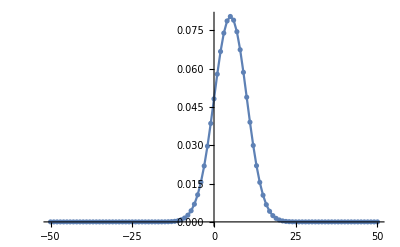

```mathematica
p=0.5; q=0.4;  n=50; m = 50; 
plotdata = Join[Table[fZm, {z,-m,-1}], Table[fZp, {z,0,n}]];
p1=ListPlot[Transpose[{Range[-m,n], plotdata}], PlotRange-> All];
p2=ListPlot[Transpose[{Range[-m,n], plotdata}], Joined-> True, PlotRange-> All];
Show[p1,p2]
```

### Compare with Monte Carlo simulation

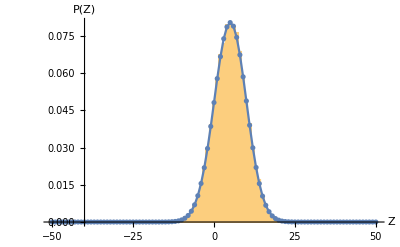

```mathematica
Xrand = RandomVariate[BinomialDistribution[n,p], 20000];
Yrand = RandomVariate[BinomialDistribution[m,q], 20000];
Zrand = Xrand - Yrand;
h1=Histogram[Zrand, {-m-0.5,n+0.5, 1}, "PDF", AxesLabel-> {"Z", "P(Z)"}, AxesOrigin->{-40,0}];
Show[h1,p1,p2]
```

## Distribution of ΔI for given Δp

(ⅇ^(-(x-μoff)^2/(2 σoff^2)))/(√(2 π) σoff (1-1/2 Erfc[(1-k+μoff)/(√2 σoff)]))

Normalized? 1

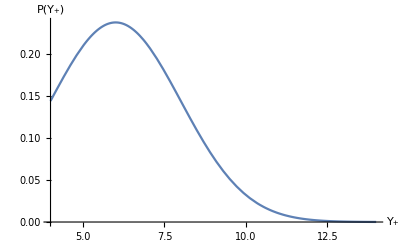

```mathematica
Yp=NormalDistribution[μoff, σoff];
fYp[x_]:=PDF[Yp, x]/(1-CDF[Yp, k-1]);
fYp[x]
Print["Normalized? ", Assuming[{μoff ∈ Reals, σoff ∈ Reals, σoff >0}, FullSimplify@Integrate[fYp[x],{x,k-1, ∞}]]
];
thisk=5;
Plot[fYp[x] /. {k->thisk, μoff -> 6, σoff -> 2},{x,thisk-1, thisk+9}, AxesLabel-> {"Y_+", "P(Y_+)"} ]
```

Current issue: code is too slow.

```mathematica
fy[n1_]:=Binomial[n, n1]  p^(n1) (1-p)^(n-n1);
p1=0.5;
n1 = 50;
k1=5;
μoff1 = 6;
σoff1 = 2;
parameters={ p->p1,  n->n1, k->k1,μoff -> μoff1, σoff -> σoff1};
fz = First@Simplify@Sum[fy[l]*fYp[x/l]*UnitStep[x/l- k +1] /.{parameters},{l,1,n}];
Print[fz]
fzvals=Table[fz /. {n-> n1}, {x,k1-1,k1-1+100, 1}]
```

∑_(l=1)^n 2.10575×10^-16 ⅇ^(-1/8 (-6+x/l)^2) Binomial[50,l] UnitStep[-4+x/l]

$Aborted